# He SCF Calculations based on STO

## Initialization

## NoteBook Options

Settings for appearance of the notebook :

```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->True];
```

## Defining Symbols

Importing Notation Package:

```mathematica
<<Notation`
```

Define spectacular symbols to use in notebook :

```mathematica
Symbolize[Subscript[V, rs]]//Quiet
Symbolize[(Ĥ)^core]//Quiet
Symbolize[Subscript[r, 1]]//Quiet
Symbolize[Subscript[r, 2]]//Quiet
Symbolize[F']//Quiet
Symbolize[C']//Quiet
Symbolize[H^core]//Quiet
Symbolize[Subscript[E, HF]]//Quiet
```

## Calculation Options

### Rationalizing

Doing calculations numerically or exact :

```mathematica
exactCalc=False;
rationalize=If[exactCalc,Rationalize[#],#]&;
```

## Common Functions

This function is needed for calculating two - electron integrals:

```mathematica
F0=If[#≠0,1/2 √(π/#)Erf[√#],1-#/3]&;
```

## Input Data

## Atoms Configuration

Importing atoms coordinates :

```mathematica
nucleiCoord=({{0.0, 0.0, 0.0}})//rationalize
```

{{0.,0.,0.}}

Atomic number of atoms:

```mathematica
Z={2}
```

{2}

Set number of atoms , basis-sets and electrons :

```mathematica
numAtoms=Length[nucleiCoord]
numBasis=2
numElectrons=2
```

1

2

2

## Basis Set Data

### Common Constants for Calculations based on STO - NG

Gaussian-type functions for 1s orbitals are defined as :
 (ϕ^GF)_(1s)[α]=((2α)/π)^(3/4) ⅇ^(-α |r-R_A|^2) 
In order to construct STO-ΝG basis set we need two sets of coefficients and exponents. The general view of a STO-3G is like this :
(ϕ^CGF)_(1s)[ζ=1.0,Ν=3]=d_13(ϕ^GF)_(1s)[α_13]+d_23(ϕ^GF)_(1s)[α_23]+d_33(ϕ^GF)_13[α_33]
Knowing d_ij’s (Coefficients) and α_ij’s  (Exponents), we can build up the contracted form of STO-ΝG.

```mathematica
((2α)/π)^(3/4)ⅇ^(-α|r-Subscript[R, A]|^2)
```

```mathematica
Manipulate[Plot[((2α)/π)^(3/4)ⅇ^(-α r^2),{r,0,10},PlotRange->{{0,10},{0,1}}],{α,0,10}]
```

Coefficient matrix (Rows are indices with respect to Ν) :

```mathematica
coef=({{1.0, 0, 0}, {0.678914, 0.430129, 0}, {0.444635, 0.535328, 0.154329}})
```

{{1.,0,0},{0.678914,0.430129,0},{0.444635,0.535328,0.154329}}

Exponent matrix (Rows are indices with respect to Ν) :

```mathematica
expon=({{0.270950, 0, 0}, {0.151623, 0.851819, 0}, {0.109818, 0.405771, 2.22766}})
```

{{0.27095,0,0},{0.151623,0.851819,0},{0.109818,0.405771,2.22766}}

```mathematica
{expon[[3]],coef[[3]]}ᵀ
```

{{0.109818,0.444635},{0.405771,0.535328},{2.22766,0.154329}}

```mathematica
(d((2α)/π)^(3/4)ⅇ^(-α r^2)/.({α->#[[1]],d->#[[2]]}&/@({expon[[3]],coef[[3]]}ᵀ)))//Total
```

0.20056 ⅇ^(-2.22766 r^2)+0.193973 ⅇ^(-0.405771 r^2)+0.0604531 ⅇ^(-0.109818 r^2)

```mathematica
gs=(d((2α)/π)^(3/4)ⅇ^(-α r^2)/.({α->#[[1]],d->#[[2]]}&/@({expon[[3]],coef[[3]]}ᵀ)))
```

{0.0604531 ⅇ^(-0.109818 r^2),0.193973 ⅇ^(-0.405771 r^2),0.20056 ⅇ^(-2.22766 r^2)}

```mathematica
gs=(d((2α)/π)^(3/4)ⅇ^(-α r^2)/.({d->#[[2]]}&/@({expon[[3]],coef[[3]]}ᵀ)))
```

```mathematica
gs={0.3168937968112911 ⅇ^(-r^2 α1) α1^(3/4),0.3815311940341962 ⅇ^(-r^2 α2) α2^(3/4),0.10999112253441529 ⅇ^(-r^2 α3) α3^(3/4)}
```

{0.316894 ⅇ^(-r^2 α1) α1^(3/4),0.381531 ⅇ^(-r^2 α2) α2^(3/4),0.109991 ⅇ^(-r^2 α3) α3^(3/4)}

```mathematica
Manipulate[Plot[Evaluate[gs],{r,0,10},PlotRange->{{0,10},{0,1}}],{α1,0,10},{α2,0,10},{α3,0,10}]
```

```mathematica
d((2α)/π)^(3/4)ⅇ^(-α r^2)/.{{α->expon[[3,1]],d->coef[[3,1]]}}
```

{0.0604531 ⅇ^(-0.109818 r^2)}

### Specific Basis Set

ζ - values based on slater type functions :

```mathematica
ζ={1.45,2.91}//rationalize
```

{1.45,2.91}

Coefficients of slater type functions :

```mathematica
a=2 ζ^(3/2)//rationalize
```

{3.49206,9.92818}

Which Basis-Set is centered on which atom?

```mathematica
basisCoord=nucleiCoord⟦{1,1}⟧
```

{{0.,0.,0.},{0.,0.,0.}}

Specify Ν value according to desired STO - ΝG :

```mathematica
Ν=3
```

3

### Calculating Basis Set Functions

#### Slater Type General Form

General type of STO basis sets :

```mathematica
slaterBasisSet[{ζ_,a_}]:=a ⅇ^(-ζ #)&
```

Populate  model basis sets with ζ and a values :

```mathematica
ϕ=Table[slaterBasisSet[{ζ,a}ᵀ⟦i⟧],{i,numBasis}]
```

{3.49206 ⅇ^(-1.45 #1)&,9.92818 ⅇ^(-2.91 #1)&}

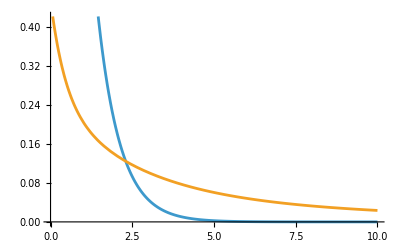

```mathematica
Plot[{ϕ[[1]][r],coef[[Ν]].(ϕGF1s[#,1]&/@expon[[Ν]])},{r,0,10}]
```

## Calculation

## Calculation of Integrals and Constant Matrices

### Calculation of S (Overlap Matrix)

#### Function for Calculating S_ij=∫ϕ_i[r-R_i]*ϕ_j[r-R_j]ⅆr for GTO (not STO)

A and B are exponents of GTO and RAB2 is distance between the center of basis set A to center of basis set B :

```mathematica
Sfunc[A_,B_,RAB2_]:=(π/(A+B))^(3/2)ⅇ^(-A B RAB2/(A+B))
```

#### Elements of S Matrix

```mathematica
S=ParallelTable[∫_0^∞ ϕ⟦i⟧[r]ϕ⟦j⟧[r] r^2 ⅆr,{i,numBasis},{j,numBasis}];
S//N//MatrixForm
```

(1. | 0.836608
0.836608 | 1.)

### Calculation of X Matrix

We use Canonical Orthogonalization here for which : 
X=U.s^(-1/2) where U†.S.U=s

#### Elements of X Matrix

If we had wanted to use Symmetric Orthogonalization (X=S^(-1/2) ):

```mathematica
X=MatrixPower[S,-1/2];
X//N//MatrixForm
```

(1.6059 | -0.868012
-0.868012 | 1.6059)

For Canonical Orthogonalization (X=U.s^(-1/2)) :

```mathematica
X=JordanDecomposition[S]/.{U_,s_}:>U. MatrixPower[s,-1/2];
X//N//MatrixForm
```

(-0.521767 | 1.74932
-0.521767 | -1.74932)

### Calculation of H^core Matrix

#### H^core Matrix ( T + ∑ V)

Defining (Ĥ)^core function for evaluation of integrals :

```mathematica
HcoreF[i_,j_]:=Piecewise[{{-1/2 ζ⟦i⟧^2+(ζ⟦i⟧-2)ζ⟦i⟧, i==j}, {-1/2 ζ⟦j⟧^2 S⟦i,j⟧+(4(ζ⟦j⟧-2)ζ⟦i⟧^(3/2)ζ⟦j⟧^(3/2))/(ζ⟦i⟧+ζ⟦j⟧)^2, True}}]
```

```mathematica
Notation[(i_|(Ĥ)^core|j_) ⟹ HcoreF[i_,j_]]
```

Calculating H^core Elements :

```mathematica
H^core=Table[(i|(Ĥ)^core|j),{i,numBasis},{j,numBasis}];
H^core//N//MatrixForm
```

(-1.84875 | -1.88258
-1.88258 | -1.58595)

```mathematica
Notation[∇_r^2 f_ ⟹ Laplacian[f_,{r,θ,ϕ0},"Spherical"]]
```

```mathematica
∇_r^2 f[r]
```

(2 f'[r])/r+f''[r]

```mathematica
∫_0^∞ (3.4920624278497656 ⅇ^(-1.45 r))(-1/2(0.+84.07278945143504 ⅇ^(-2.91 r)+(0.-28.89099293863747 ⅇ^(-2.91 r))/r+(Csc[θ] (0.-28.89099293863747 ⅇ^(-2.91 r) Sin[θ]))/r)-(19.856352535146026 ⅇ^(-2.91 r))/r)r^2 ⅆr
```

-1.88258

## Initial Guess

### Custom Initial Guess

We can specify custom initial values for Ć matrix and ignoring calculation of the initial guess using H^core≈F.

```mathematica
Ć=({{0.842, 0.183}, {0.18413, 0.842}})
```

{{0.842,0.183},{0.18413,0.842}}

### Initial Guess using F ≈ H^core Approximation

#### Calculation of ℋ (Orthonormal form of H^core)

Diagonalizing ℋ using X Matrix :

```mathematica
ℋ=X†.(H^core).X;
ℋ//N//MatrixForm
```

(-0.7143 | -1.48566
-1.48566 | -0.234564)

#### Diagonalizing ℋ

By this diagonalization we obtain initial guess for Matrix Ć :

First, Diagonalization to ℭ':

```mathematica
{ℭ',ε}=JordanDecomposition[ℋ];
ℭ'//N//MatrixForm
```

(-0.761377 | 0.648309
-0.648309 | -0.761377)

Second, Converting ℭ'back to Ć

```mathematica
Ć=X.ℭ';
Ć//N//MatrixForm
```

(-0.659957 | 1.70201
-0.380236 | -1.78544)

Although not useful, Showing obtained ε Matrix :

```mathematica
ε//N//MatrixForm
```

(-1.97933 | 0.
0. | 1.03047)

And Just a look at a typical value showing the order of error (It would be zero, if we set exactCalc to True):

```mathematica
Norm[ℭ'.ε.Inverse[ℭ']-ℋ]
```

5.8132×10^-16

## Iterating Section Calculation

### Calculation of P Matrix (Density Matrix) from Ć Matrix

Getting P matrix from Ć , using :

```mathematica
P=2Table[∑_(a=1)^(numElectrons/2) Ć⟦μ,a⟧**Ć⟦ν,a⟧,{μ,numBasis},{ν,numBasis}];
P//N//MatrixForm
```

(1.41793 | 0.310075
0.310075 | 0.0678077)

### Calculation of G Matrix

#### Calculation of Two-Electron Integrals

Defining a function to calculate Integrals of the form:

∫_0^∞ ∫_0^∞ ϕ_i[r_1-R_A]*ϕ_j[r_1-R_B](1/r_12)ϕ_k[r_2-R_Ć]*ϕ_l[r_2-R_D] r_1^2 r_2^2 ⅆ r_1ⅆ r_2

A,B,Ć,D are exponents of the four ϕ GTOs ; RAB2 and RCD2 are square of the distance between the corresponding center of ϕ GTOs ; and P and Q are calculated using R_P=(A R_A+B R_B)/(A+B) and R_Q=(Ć R_Ć+D R_D)/(Ć+D) , respectively.

```mathematica
twoEfunc[i_,j_,k_,l_]:=Piecewise[{{5/8 ζ⟦i⟧, i==j==k==l}, {(ζ⟦i⟧^4 ζ⟦k⟧^1+4 ζ⟦i⟧^3 ζ⟦k⟧^2+ζ⟦i⟧^1 ζ⟦k⟧^4+4 ζ⟦i⟧^2 ζ⟦k⟧^3)/((ζ⟦i⟧^1+ζ⟦k⟧^1)^4), i==j&&k==l&&i≠k}, {(20 ζ⟦i⟧^3 ζ⟦j⟧^3)/((ζ⟦i⟧^1+ζ⟦j⟧^1)^5), i≠j&&k≠l}, {(16 ζ⟦j⟧^(9/2)ζ⟦i⟧^(3/2))/((3 ζ⟦j⟧^1+ζ⟦i⟧^1)^4)((12 ζ⟦j⟧^1+8 ζ⟦i⟧^1)/((ζ⟦j⟧^1+ζ⟦i⟧^1)^2)+(9 ζ⟦j⟧^1+ζ⟦i⟧^1)/(2(ζ⟦j⟧^1)^2)), i≠j&&k==l≠i}, {(16 ζ⟦i⟧^(9/2)ζ⟦j⟧^(3/2))/((3 ζ⟦i⟧^1+ζ⟦j⟧^1)^4)((12 ζ⟦i⟧^1+8 ζ⟦j⟧^1)/((ζ⟦i⟧^1+ζ⟦j⟧^1)^2)+(9 ζ⟦i⟧^1+ζ⟦j⟧^1)/(2(ζ⟦i⟧^1)^2)), i≠j&&k==l≠j}, {(16 ζ⟦l⟧^(9/2)ζ⟦k⟧^(3/2))/((3 ζ⟦l⟧^1+ζ⟦k⟧^1)^4)((12 ζ⟦l⟧^1+8 ζ⟦k⟧^1)/((ζ⟦l⟧^1+ζ⟦k⟧^1)^2)+(9 ζ⟦l⟧^1+ζ⟦k⟧^1)/(2(ζ⟦l⟧^1)^2)), k≠l&&i==j≠k}, {(16 ζ⟦k⟧^(9/2)ζ⟦l⟧^(3/2))/((3 ζ⟦k⟧^1+ζ⟦l⟧^1)^4)((12 ζ⟦k⟧^1+8 ζ⟦l⟧^1)/((ζ⟦k⟧^1+ζ⟦l⟧^1)^2)+(9 ζ⟦k⟧^1+ζ⟦l⟧^1)/(2(ζ⟦k⟧^1)^2)), k≠l&&i==j≠l}}]
```

We could have used of explicit integral calculations, but it would be taken much longer time. Now we’ll formulate the explicit integral form and obtain the numerical value of it just for representation purposes:

```mathematica
twoEfuncExplicit[i_,j_,k_,l_]:=∫_0^∞ ∫_0^∞ ϕ⟦i⟧[Subscript[r, 1]]*ϕ⟦j⟧[Subscript[r, 1]] 1/Max[{Subscript[r, 1],Subscript[r, 2]}] ϕ⟦k⟧[Subscript[r, 2]]*ϕ⟦l⟧[Subscript[r, 2]] Subscript[r, 1]^2 Subscript[r, 2]^2 ⅆ Subscript[r, 1]ⅆ Subscript[r, 2]
```

```mathematica
Module[{i=1,j=2,k=1,l=1},{twoEfunc[i,j,k,l],twoEfuncExplicit[i,j,k,l]}
]
```

{0.903281,0.903281}

Defining chemists’ notation of two-electron integrals :

```mathematica
Notation[(i_,j_|k_,l_) ⟹ twoEfunc[i_,j_,k_,l_]]
```

Calculating  all different sets of two - electron integrals :

```mathematica
twoEInt=Table[(ι,κ|ς,ϑ),{ι,numBasis},{κ,numBasis},{ς,numBasis},{ϑ,numBasis}]//Chop;
(MatrixForm/@twoEInt)//N//MatrixForm
```

(((0.90625
0.903281) | (0.903281
1.18259)
(0.903281
0.953631) | (0.953631
1.298))
((0.903281
0.953631) | (0.953631
1.298)
(1.18259
1.298) | (1.298
1.81875)))

Calculation of G matrix elements :

```mathematica
G=Table[∑_(λ=1)^numBasis ∑_(σ=1)^numBasis P⟦λ,σ⟧((μ,ν|σ,λ)-1/2(μ,λ|σ,ν)),{μ,numBasis},{ν,numBasis}];
G//N//MatrixForm
```

(0.97044 | 0.944601
0.944601 | 1.46487)

### Calculation of F Matrix (Fock Operator)

According to the Equation F=H^core+G :

```mathematica
F=H^core+G;
F//N//MatrixForm
```

(-0.87831 | -0.937976
-0.937976 | -0.121075)

### Calculation of F' Matrix (Transformed Fock Matrix)

Now, transforming F to F' using the equation : F'=S^(-1/2).F.S^(-1/2)

```mathematica
F'=MatrixPower[S,-1/2].F.MatrixPower[S,-1/2];
F'//N//MatrixForm
```

(0.258654 | -1.7326
-1.7326 | 1.64097)

### Diagonalizing F' to obtain ℭ' and ε

Diagonalizing is done by a function called JordanDecomposition :

```mathematica
{ℭ',ε}=JordanDecomposition[F']/.{c_,e_}:>{c,Reverse/@((Reverse/@e)ᵀ)};
MatrixForm/@{ℭ',ε}//N
```

{(-0.561016 | -0.827805
0.827805 | -0.561016),(-0.915554 | 0.
0. | 2.81518)}

### Convert ℭ' Back to Ć

According to Ć=S^(-1/2).C':

```mathematica
Ć=MatrixPower[S,-1/2].ℭ';
Ć//N//MatrixForm
```

(-1.61948 | -0.842404
1.81634 | -0.182393)

### Calculate the new P Matrix from Ć

This calculation is done just for checking convergence :

```mathematica
Ćrot=Reverse/@Ć
newP=2Table[∑_(a=1)^(numElectrons/2) Ćrot⟦μ,a⟧**Ćrot⟦ν,a⟧,{μ,numBasis},{ν,numBasis}];
MatrixForm/@{newP,P}//N
```

{{-0.842404,-1.61948},{-0.182393,1.81634}}

{(1.41929 | 0.307298
0.307298 | 0.0665345),(1.41793 | 0.310075
0.310075 | 0.0678077)}

### Determine Convergence Criterion

Here we use the norm of the P_new-P_old as a criterion for checking convergence :

```mathematica
Norm[P-newP ]//N
```

0.00311854

### Calculating E_0 and E_total

#### E_0

We use the old P Matrix to calculate the electronic energy of molecule .
The equation is :
E_0=1/2∑_(μ=1)^numBasis ∑_(ν=1)^numBasis P_(ν,μ)((H^core)_(μ,ν)+F_(μ,ν))

```mathematica
ElecE=1/2 P(H^core+F) //Total[#,2]&
```

-2.86584

#### E_total

The electronic energy plus the repulsion of nucleus gives up the total energy ( except ZPE ) :

```mathematica
TotalE=ElecE+If[numElectrons≥2,∑_(μ=1)^numAtoms ∑_(ν=μ+1)^numAtoms ((Z⟦μ⟧Z⟦ν⟧)/Norm[nucleiCoord⟦μ⟧-nucleiCoord⟦ν⟧]^2),0]
```

-2.77633

## Results

Here the P,G,F,F',Ć,ε,E_0,E_total for each iteration is shown and updated automatically :

```mathematica
results=Dataset[<|1->AssociationThread[{"P","G","F","F'","Ć","ε","E_elec","E_total"}->MatrixForm/@{P,G,F,F',Ć,ε,ElecE,TotalE}]|>];
results//Dynamic
```

## Automatic Iterations

This set of code is written in order to automatically do the iterations until reaches the convergence criterion.

### Settings

Number of iterations done up until now :

```mathematica
iter=1
```

1

Max iterations allowed :

```mathematica
maxIter=100
```

100

Allowance limit of Norm[P_old-P_new] :

```mathematica
plim=10.^-7//rationalize
```

1.×10^-7

### Iterative Loop

```mathematica
While[Norm[P-newP//N]≥plim&&iter≤maxIter,
iter+=1;
P=newP;
G=Table[∑_(λ=1)^numBasis ∑_(σ=1)^numBasis P⟦λ,σ⟧((μ,ν|σ,λ)-1/2(μ,λ|σ,ν)),{μ,numBasis},{ν,numBasis}];
F=H^core+G;
F'=MatrixPower[S,-1/2].F.MatrixPower[S,-1/2];
{ℭ',ε}=JordanDecomposition[F']/.{c_,e_}:>{c,Reverse/@((Reverse/@e)ᵀ)};
Ć=MatrixPower[S,-1/2].ℭ';
Ćrot=Reverse/@Ć;
newP=2Table[∑_(a=1)^(numElectrons/2) Ćrot⟦μ,a⟧**Ćrot⟦ν,a⟧,{μ,numBasis},{ν,numBasis}];
ElecE=1/2 P(H^core+F) //Total[#,2]&;
TotalE=ElecE+If[numElectrons≥2,∑_(μ=1)^numAtoms ∑_(ν=μ+1)^numAtoms ((Z⟦μ⟧Z⟦ν⟧)/Norm[nucleiCoord⟦μ⟧-nucleiCoord⟦ν⟧]^2),0];
AppendTo[results,<|iter->AssociationThread[{"P","G","F","F'","Ć","ε","E_elec","E_total"}->MatrixForm/@{P,G,F,F',Ć,ε,ElecE,TotalE}]|>];
]
```

## Population Analysis

## Total Number of Electrons

```mathematica
∑_(ν=1)^numBasis ∑_(μ=1)^numBasis P⟦ν,μ⟧S⟦ν,μ⟧
```

2.